## Dynamical Phases (Θ)

### SM Phase

```mathematica
(*Neutrino mixing angles*)θ12=34.0 Degree;
θ23=40.0 Degree;
θ13=9.0 Degree;

(*Neutrino mixing matrix elements*)
Upmns={{Cos[θ12] Cos[θ13],Sin[θ12] Cos[θ13],Sin[θ13]},{-Sin[θ12] Cos[θ23]-Cos[θ12] Sin[θ23] Sin[θ13],Cos[θ12] Cos[θ23]-Sin[θ12] Sin[θ23] Sin[θ13],Sin[θ23] Cos[θ13]},{Sin[θ12] Sin[θ23]-Cos[θ12] Cos[θ23] Sin[θ13],-Cos[θ12] Sin[θ23]-Sin[θ12] Cos[θ23] Sin[θ13],Cos[θ23] Cos[θ13]}};
```

```mathematica
SMTheta[x_,E1_]:=Upmns[[1,1]]^2 * m1^2/(2E1)*x +Upmns[[1,2]]^2 *m2^2/(2E1)*x +Upmns[[1,3]]^2 *m3^2/(2E1)*x ;
```

```mathematica
m1no=0.0298;m2no=0.031;m3no=0.0589(* ∑ Subscript[m, i]<= 0.12 Normal Ordering*); 
m1io=0.0157;m2io=0.0517;m3io=0.0525;(* ∑ Subscript[m, i]<= 0.12 Normal Ordering*)
```

```mathematica
m1=m1no;m2=m2no;m3=m3no;(*m (eV), L (Km), E (GeV)*)
```

### CW Phase

```mathematica
n=39;q=2;(*m (eV), L (Km), E (GeV)*)(*m (eV), L (Km), E (GeV)*)
v=173*Power[10,9]; m =1*Power[10,12] (*1 TeV*);
 y1=0.1*1.1;y2=0.1*1.15;y3=0.1*2.15;
```

```mathematica
p=y1*v/m;p2=y2*v/m;p3=y3*v/m;
```

```mathematica
lambda = Table[1+q^2-2q*Cos[i*π/(n+1)],{i,1,n}]
```

{5-4 cos(π/40),5-4 cos(π/20),5-4 cos((3 π)/40),5-4 √(5/8+(√5)/8),5-4 cos(π/8),5-4 cos((3 π)/20),5-4 cos((7 π)/40),4-√5,5-4 cos((9 π)/40),5-2 √2,5-4 sin((9 π)/40),5-4 √(5/8-(√5)/8),5-4 sin((7 π)/40),5-4 sin((3 π)/20),5-4 sin(π/8),6-√5,5-4 sin((3 π)/40),5-4 sin(π/20),5-4 sin(π/40),5,5+4 sin(π/40),5+4 sin(π/20),5+4 sin((3 π)/40),4+√5,5+4 sin(π/8),5+4 sin((3 π)/20),5+4 sin((7 π)/40),5+4 √(5/8-(√5)/8),5+4 sin((9 π)/40),5+2 √2,5+4 cos((9 π)/40),6+√5,5+4 cos((7 π)/40),5+4 cos((3 π)/20),5+4 cos(π/8),5+4 √(5/8+(√5)/8),5+4 cos((3 π)/40),5+4 cos(π/20),5+4 cos(π/40)}

```mathematica
Ccomp=Table[2*q^2/(lambda[[i]])*Sin[(n*i*π)/(n+1)]^2,{i,1,n}]
```

{(8 sin^2(π/40))/(5-4 cos(π/40)),(8 sin^2(π/20))/(5-4 cos(π/20)),(8 sin^2((3 π)/40))/(5-4 cos((3 π)/40)),(1-√5)^2/(2 (5-4 √(5/8+(√5)/8))),(8 sin^2(π/8))/(5-4 cos(π/8)),(8 sin^2((3 π)/20))/(5-4 cos((3 π)/20)),(8 sin^2((7 π)/40))/(5-4 cos((7 π)/40)),(8 (5/8-(√5)/8))/(4-√5),(8 sin^2((9 π)/40))/(5-4 cos((9 π)/40)),4/(5-2 √2),(8 cos^2((9 π)/40))/(5-4 sin((9 π)/40)),(-1-√5)^2/(2 (5-4 √(5/8-(√5)/8))),(8 cos^2((7 π)/40))/(5-4 sin((7 π)/40)),(8 cos^2((3 π)/20))/(5-4 sin((3 π)/20)),(8 cos^2(π/8))/(5-4 sin(π/8)),(8 (5/8+(√5)/8))/(6-√5),(8 cos^2((3 π)/40))/(5-4 sin((3 π)/40)),(8 cos^2(π/20))/(5-4 sin(π/20)),(8 cos^2(π/40))/(5-4 sin(π/40)),8/5,(8 cos^2(π/40))/(5+4 sin(π/40)),(8 cos^2(π/20))/(5+4 sin(π/20)),(8 cos^2((3 π)/40))/(5+4 sin((3 π)/40)),(8 (5/8+(√5)/8))/(4+√5),(8 cos^2(π/8))/(5+4 sin(π/8)),(8 cos^2((3 π)/20))/(5+4 sin((3 π)/20)),(8 cos^2((7 π)/40))/(5+4 sin((7 π)/40)),(-1-√5)^2/(2 (5+4 √(5/8-(√5)/8))),(8 cos^2((9 π)/40))/(5+4 sin((9 π)/40)),4/(5+2 √2),(8 sin^2((9 π)/40))/(5+4 cos((9 π)/40)),(8 (5/8-(√5)/8))/(6+√5),(8 sin^2((7 π)/40))/(5+4 cos((7 π)/40)),(8 sin^2((3 π)/20))/(5+4 cos((3 π)/20)),(8 sin^2(π/8))/(5+4 cos(π/8)),(1-√5)^2/(2 (5+4 √(5/8+(√5)/8))),(8 sin^2((3 π)/40))/(5+4 cos((3 π)/40)),(8 sin^2(π/20))/(5+4 cos(π/20)),(8 sin^2(π/40))/(5+4 cos(π/40))}

```mathematica
U10=1-p^2/(n+1) *Sum[Ccomp[[i]]/(2*lambda[[i]]),{i,1,n}] (*p = yv/m < 1*)
```

0.99994

```mathematica
U1j=Table[-p*Sqrt[Ccomp[[i]]/((n+1)*lambda[[i]])],{i,1,n}]
```

{-0.000659591,-0.00126885,-0.00178901,-0.00219931,-0.00249664,-0.00269063,-0.00279766,-0.0028359,-0.00282229,-0.00277118,-0.00269395,-0.00259928,-0.00249359,-0.00238153,-0.00226637,-0.0021504,-0.00203514,-0.00192163,-0.00181049,-0.00170209,-0.00159663,-0.00149415,-0.00139461,-0.00129792,-0.00120395,-0.00111252,-0.00102347,-0.000936605,-0.00085175,-0.000768713,-0.000687313,-0.000607369,-0.000528706,-0.000451152,-0.00037454,-0.000298707,-0.000223492,-0.00014874,-0.0000742934}

```mathematica
masscw=Table[m*Sqrt[lambda[[i]](1+ p^2*Ccomp[[i]]/(2(n+1)lambda[[i]]))],{i,1,n}];
```

```mathematica
U2j =U1j/.p->p2;
U3j =U1j/.p->p3;
U20 =U10/.p->p2;
U30 =U10/.p->p3;
masscw2=masscw/.p->p2;
masscw3=masscw/.p->p3;
```

```mathematica
massdivE={m1^2/(2*E1),Table[masscw[[i]]^2/(2*E1),{i,1,n}]}//Flatten;
massdivE2=massdivE /.p->p2;
massdivE3=massdivE /.p->p3;
```

```mathematica
Upmns
```

(0.818831 | 0.552308 | 0.156434
-0.51173 | 0.57885 | 0.634874
0.260094 | -0.599906 | 0.756613)

```mathematica
Utot1=Flatten[{U10,U1j}];
Utot2=Flatten[{U20,U2j}];
Utot3=Flatten[{U30,U3j}];
```

```mathematica
CWTheta[t_,E2_]:=((Evaluate[Sum[Utot1[[i]]^2*massdivE[[i]],{i,1,n+1}]*Upmns[[1,1]]^2+Sum[Utot2[[i]]^2*massdivE2[[i]],{i,1,n+1}]*Upmns[[1,2]]^2+Sum[Utot3[[i]]^2*massdivE3[[i]],{i,1,n+1}]*Upmns[[1,3]]^2] /.E1->E2))*t
```

```mathematica
CW[t_,E2_]:=Evaluate[CWTheta[t,E2]]
```

### Sterile Phase

```mathematica
Usterile=0.01;ms=10;(*m (eV), L (Km), E (GeV)*)
```

```mathematica
SterileTheta[x_,E1_]:=Upmns[[1,1]]^2 * m1^2/(2E1)*x +Upmns[[1,2]]^2 *m2^2/(2E1)*x +Upmns[[1,3]]^2 *m3^2/(2E1)*x +Usterile^2 *( ms^2/(2E1))*x ;
```

```mathematica
SterileTheta[x,y]
```

(0.00548673 x)/y

### Extra Dimension Phase (Approx.)

```mathematica
Clear[m1ED,m2ED,m3ED,RED,n]
```

```mathematica
R=1 (*Same as RED*);En=Power[10,13] (*GeV*);ned=0.01En*R;
```

```mathematica
massED01=m1ED(1-(π^2/6)*(m1ED*RED)^2);
massED02=massED01/.m1ED->m2ED;
massED02=massED01/.m1ED->m3ED;
```

```mathematica
UEDi01=Sqrt[1/(1+1/3*π^2(m1ED*RED)^2)];
UEDi02=UEDi01/.m1ED->m2ED;
UEDi03=UEDi01/.m1ED->m3ED;
```

```mathematica
massdivEED01=UEDi01^2massED01^2/(2*E1);
massdivEED02=massdivEED01/.m1ED->m2ED;
massdivEED03=massdivEED01/.m1ED->m3ED;
```

```mathematica
massdivEEDi1=2m1ED^2/(2*E1);
massdivEEDi2=massdivEEDi1/.m1ED->m2ED;
massdivEEDi3=massdivEEDi1/.m1ED->m3ED;
```

```mathematica
EDThetaapprox[t_,E2_]:=((Evaluate[massdivEED01*Upmns[[1,1]]^2+massdivEED02*Upmns[[1,2]]^2+massdivEED03*Upmns[[1,3]]^2+ned*massdivEEDi1*Upmns[[1,1]]^2+ned*massdivEEDi2*Upmns[[1,2]]^2+ned*massdivEEDi3*Upmns[[1,3]]^2] /.E1->E2))*t
```

```mathematica
m1ED=m1;m2ED=m2;m3ED=m3; (*mR<<1*)RED=1(*1 eV^-1 = 1 μm*);
```

```mathematica
EDapp[x_,y_]:=Evaluate[EDThetaapprox[x,y]];
```

### Extra Dimension Phase (Exact)

```mathematica
Clear[m1ED,m2ED,m3ED,RED,n]
```

```mathematica
R=1 (*Same as RED*);En=Power[10,13] (*GeV*);ned=0.0000000001En*R;
```

```mathematica
massEDi=ParallelTable[(i/RED)(1+(m1ED*RED)^2/(i^2)),{i,1,ned}];(*m (eV), L (Km), E (GeV)*)
massED0=m1ED(1-(π^2/6)*(m1ED*RED)^2);
```

```mathematica
massED={massED0,ParallelTable[massEDi[[i]],{i,1,ned}]}//Flatten;
massED2=massED/.m1ED->m2ED;
massED3=massED/.m1ED->m2ED;
```

```mathematica
UEDij=ParallelTable[Sqrt[2/(1+π^2(m1ED*RED)^2+(massED[[i]]/m1ED)^2)],{i,1,ned+1}];
UEDij2=UEDij/.m1ED->m2ED;
UEDij3=UEDij/.m1ED->m3ED;
```

```mathematica
massdivEED=ParallelTable[massED[[i]]^2/(2*E1),{i,1,ned+1}];
massdivEED2=massdivEED/.m1ED->m2ED;
massdivEED3=massdivEED/.m1ED->m3ED;
```

```mathematica
EDTheta[t_,E2_]:=((Evaluate[Sum[UEDij[[i]]^2*massdivEED[[i]],{i,1,ned+1}]*Upmns[[1,1]]^2+Sum[UEDij2[[i]]^2*massdivEED2[[i]],{i,1,ned+1}]*Upmns[[1,2]]^2+Sum[UEDij3[[i]]^2*massdivEED3[[i]],{i,1,ned+1}]*Upmns[[1,3]]^2] /.E1->E2))*t
```

```mathematica
m1ED=m1;m2ED=m2;m3ED=m3; (*mR<<1*)RED=1(*1 eV^-1 = 1 μm*);
```

```mathematica
ED[x_,y_]:=Evaluate[EDTheta[x,y]];
```

### Pseudo-Dirac Phase

```mathematica
f[x_]:=Mod[x,360]
g[x_]:=Mod[x+x,360]
```

```mathematica
m1pd=0.01*m1;m2pd=0.01*m2;m3pd=0.01*m3;(*m (eV), L (Km), E (GeV)*)
```

```mathematica
PDTheta[x_,E1_]:=Upmns[[1,1]]^2 * m1^2/(2E1)*x +Upmns[[1,2]]^2 *m2^2/(2E1)*x +Upmns[[1,3]]^2 *m3^2/(2E1)*x +Upmns[[1,1]]^2 * m1pd^2/(2E1)*x +Upmns[[1,2]]^2 *m2pd^2/(2E1)*x +Upmns[[1,3]]^2 *m3pd^2/(2E1)*x ;
```

### All Theta Phases

```mathematica
SMTheta[x,1]/.x->100
```

0.0486731

```mathematica
CW[x,1]
```

1.81071×10^20 x

```mathematica
PDTheta[x,1]/.x->100
```

0.048678

```mathematica
SterileTheta[x,1]/.x->100
```

0.548673

```mathematica
Energy = 100000; (*GeV*)
```

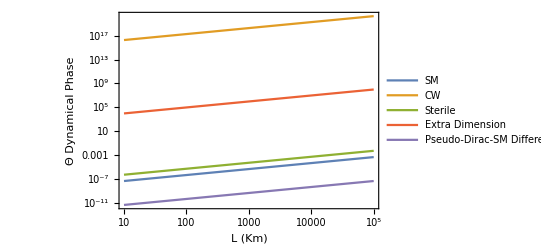

```mathematica
LogLogPlot[{SMTheta[x,Energy],CW[x,Energy],SterileTheta[x,Energy],EDapp[x,Energy],-SMTheta[x,Energy]+PDTheta[x,Energy]},{x,10,100000},PlotLegends->LineLegend[{"SM","CW","Sterile","Extra Dimension","Pseudo-Dirac-SM \n Difference"},LegendFunction->(Framed[#,RoundingRadius->10]&),LabelStyle->{FontSize->7}],PlotRange->All,Frame->True,FrameLabel->{Style["L (Km)",Black,FontSize->10],Style["Θ Dynamical Phase",Black,FontSize->10]},FrameTicksStyle->Black,LabelStyle->{FontSize->12}]
```

## Total Phases (ϕ)

### SM Phase

```mathematica
(*Neutrino mixing angles*)θ12=34.0 Degree;
θ23=40.0 Degree;
θ13=9.0 Degree;

(*Neutrino mixing matrix elements*)
Upmns={{Cos[θ12] Cos[θ13],Sin[θ12] Cos[θ13],Sin[θ13]},{-Sin[θ12] Cos[θ23]-Cos[θ12] Sin[θ23] Sin[θ13],Cos[θ12] Cos[θ23]-Sin[θ12] Sin[θ23] Sin[θ13],Sin[θ23] Cos[θ13]},{Sin[θ12] Sin[θ23]-Cos[θ12] Cos[θ23] Sin[θ13],-Cos[θ12] Sin[θ23]-Sin[θ12] Cos[θ23] Sin[θ13],Cos[θ23] Cos[θ13]}};
```

```mathematica
SMphi[x_,E1_]:=ArcTan[Upmns[[1,1]]^2 *Cos[ 1.27m1^2x/(E1)] +Upmns[[1,2]]^2 *Cos[1.27m2^2/(2E1)*x ]+Upmns[[1,3]]^2 *Cos[1.27m3^2/(2E1)*x],-Upmns[[1,1]]^2 *Sin[ 1.27m1^2x/(E1)] -Upmns[[1,2]]^2 *Sin[1.27m2^2/(2E1)*x ]-Upmns[[1,3]]^2 *Sin[1.27m3^2/(2E1)*x] ];
```

```mathematica
m1no=0.0298;m2no=0.031;m3no=0.0589(* ∑ Subscript[m, i]<= 0.12 Normal Ordering*); 
m1io=0.0157;m2io=0.0517;m3io=0.0525;(* ∑ Subscript[m, i]<= 0.12 Normal Ordering*)
```

```mathematica
m1=m1no;m2=m2no;m3=m3no;(*m (eV), L (Km), E (GeV)*)
```

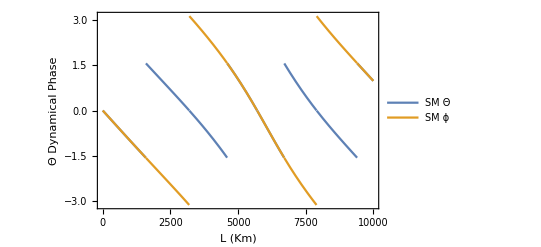

```mathematica
Plot[{ArcTan[Tan[SMphi[x,1]]],SMphi[x,1]},{x,0,010000},PlotLegends->LineLegend[{"SM Θ","SM ϕ","SM Φ"},LegendFunction->(Framed[#,RoundingRadius->10]&),LabelStyle->{FontSize->7}],PlotRange->All,Frame->True,FrameLabel->{Style["L (Km)",Black,FontSize->10],Style["Θ Dynamical Phase",Black,FontSize->10]},FrameTicksStyle->Black,LabelStyle->{FontSize->12}]
```

```mathematica
SMphi[10000x,1]
Sterilephi[x,1]
```

tan^-1(0.305044 cos(6.10235 x)+0.670484 cos(11.2781 x)+0.0244717 cos(22.0295 x),-0.305044 sin(6.10235 x)-0.670484 sin(11.2781 x)-0.0244717 sin(22.0295 x))

tan^-1(0.305044 cos(0.000610235 x)+0.670484 cos(0.00112781 x)+0.0244717 cos(0.00220295 x)+0.0001 cos(63.5 x),-0.305044 sin(0.000610235 x)-0.670484 sin(0.00112781 x)-0.0244717 sin(0.00220295 x)-0.0001 sin(63.5 x))

### Sterile Phase

```mathematica
Usterile=0.01;ms=10;(*m (eV), L (Km), E (GeV)*)
```

```mathematica
Sterilephi[x_,E1_]:=ArcTan[Upmns[[1,1]]^2 *Cos[ 1.27m1^2x/(E1)] +Upmns[[1,2]]^2 *Cos[1.27m2^2/(2E1)*x ]+Upmns[[1,3]]^2 *Cos[1.27m3^2/(2E1)*x]+Usterile^2 *Cos[( 1.27ms^2/(2E1))*x],-Upmns[[1,1]]^2 *Sin[ 1.27m1^2x/(E1)] -Upmns[[1,2]]^2 *Sin[1.27m2^2/(2E1)*x ]-Upmns[[1,3]]^2 *Sin[1.27m3^2/(2E1)*x]-Usterile^2 *Sin[(1.27 ms^2/(2E1))*x] ];
```

```mathematica
Sterilephi[x,y]
```

tan^-1(0.305044 cos((0.000610235 x)/y)+0.670484 cos((0.00112781 x)/y)+0.0244717 cos((0.00220295 x)/y)+0.0001 cos((63.5 x)/y),-0.305044 sin((0.000610235 x)/y)-0.670484 sin((0.00112781 x)/y)-0.0244717 sin((0.00220295 x)/y)-0.0001 sin((63.5 x)/y))

### All Theta Phases

```mathematica
Energy = 10; (*GeV*)
```

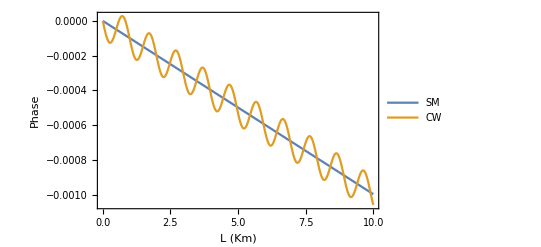

```mathematica
Plot[{SMphi[x,Energy],Sterilephi[x,Energy]},{x,00,010},PlotRange->All,PlotLegends->LineLegend[{"SM","CW","Sterile","Extra Dimension","Pseudo-Dirac-SM \n Difference"},LegendFunction->(Framed[#,RoundingRadius->10]&),LabelStyle->{FontSize->7}],PlotRange->All,Frame->True,FrameLabel->{Style["L (Km)",Black,FontSize->10],Style["Phase",Black,FontSize->10]},FrameTicksStyle->Black,LabelStyle->{FontSize->12}]
```

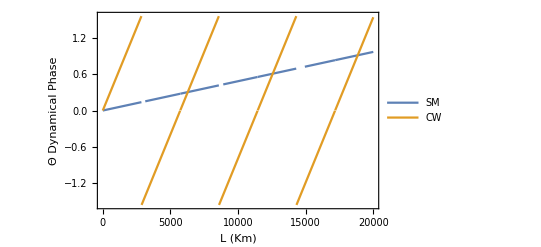

```mathematica
Plot[{ArcTan[Tan[SMTheta[x,Energy]]],ArcTan[Tan[SterileTheta[x,Energy]]]},{x,1,20000},PlotLegends->LineLegend[{"SM","CW","Sterile","Extra Dimension","Pseudo-Dirac-SM \n Difference"},LegendFunction->(Framed[#,RoundingRadius->10]&),LabelStyle->{FontSize->7}],PlotRange->All,Frame->True,FrameLabel->{Style["L (Km)",Black,FontSize->10],Style["Θ Dynamical Phase",Black,FontSize->10]},FrameTicksStyle->Black,LabelStyle->{FontSize->12}]
```

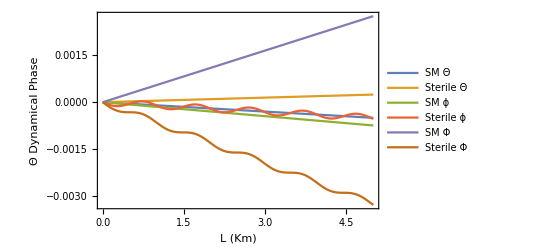

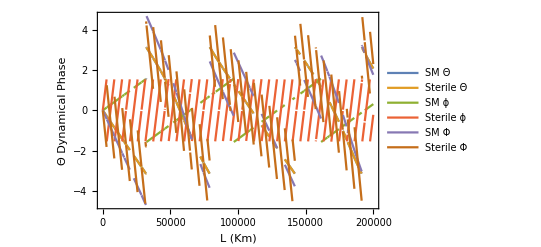

```mathematica
Plot[{SMphi[x,Energy],SMTheta[x,Energy],SMphi[x,Energy]-SMTheta[x,Energy],Sterilephi[x,Energy],SterileTheta[x,Energy],Sterilephi[x,Energy]-SterileTheta[x,Energy]},{x,0.001,5},PlotLegends->LineLegend[{"SM Θ","Sterile Θ","SM ϕ","Sterile ϕ","SM Φ","Sterile Φ"},LegendFunction->(Framed[#,RoundingRadius->10]&),LabelStyle->{FontSize->7}],PlotRange->All,Frame->True,FrameLabel->{Style["L (Km)",Black,FontSize->10],Style["Θ Dynamical Phase",Black,FontSize->10]},FrameTicksStyle->Black,LabelStyle->{FontSize->12}]
Plot[{SMphi[x,Energy],Sterilephi[x,Energy],ArcTan[Tan[SMTheta[x,Energy]]],ArcTan[Tan[SterileTheta[x,Energy]]],SMphi[x,Energy]-ArcTan[Tan[SMTheta[x,Energy]]],Sterilephi[x,Energy]-ArcTan[Tan[SterileTheta[x,Energy]]]},{x,01,200000},PlotLegends->LineLegend[{"SM Θ","Sterile Θ","SM ϕ","Sterile ϕ","SM Φ","Sterile Φ"},LegendFunction->(Framed[#,RoundingRadius->10]&),LabelStyle->{FontSize->7}],PlotRange->All,Frame->True,FrameLabel->{Style["L (Km)",Black,FontSize->10],Style["Θ Dynamical Phase",Black,FontSize->10]},FrameTicksStyle->Black,LabelStyle->{FontSize->12}]
```

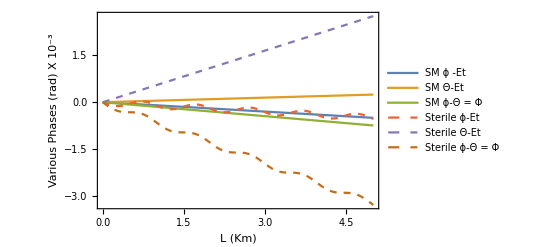

```mathematica
Energy=10;tempnum=1000;
Plot[{tempnum*SMphi[x,Energy],tempnum*SMTheta[x,Energy],tempnum*SMphi[x,Energy]-tempnum*SMTheta[x,Energy],tempnum*Sterilephi[x,Energy],tempnum*SterileTheta[x,Energy],tempnum*Sterilephi[x,Energy]-tempnum*SterileTheta[x,Energy]},{x,0.001,5},PlotStyle->{Thick,Thick,Thick,{Dashed,Thick},{Dashed,Thick},{Dashed,Thick}},PlotLegends->LineLegend[{"SM ϕ -Et","SM Θ-Et","SM ϕ-Θ = Φ","Sterile ϕ-Et","Sterile Θ-Et","Sterile ϕ-Θ = Φ"},LegendFunction->(Framed[#,RoundingRadius->10]&),LabelStyle->{FontSize->7}],PlotRange->All,Frame->True,FrameLabel->{Style["L (Km)",Black,FontSize->10],Style["Various Phases (rad) X 10^-3",Black,FontSize->10]},FrameTicksStyle->Black,LabelStyle->{FontSize->12}]
```

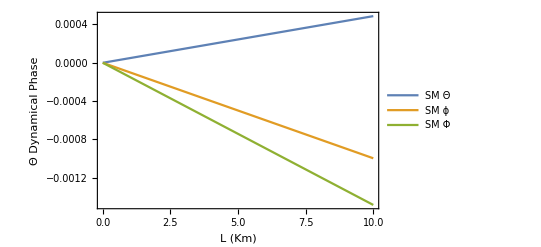

```mathematica
Plot[{ArcTan[Tan[SMTheta[x,Energy]]],SMphi[x,Energy],SMphi[x,Energy]-ArcTan[Tan[SMTheta[x,Energy]]]},{x,0,10},PlotLegends->LineLegend[{"SM Θ","SM ϕ","SM Φ"},LegendFunction->(Framed[#,RoundingRadius->10]&),LabelStyle->{FontSize->7}],PlotRange->All,Frame->True,FrameLabel->{Style["L (Km)",Black,FontSize->10],Style["Θ Dynamical Phase",Black,FontSize->10]},FrameTicksStyle->Black,LabelStyle->{FontSize->12}]
```

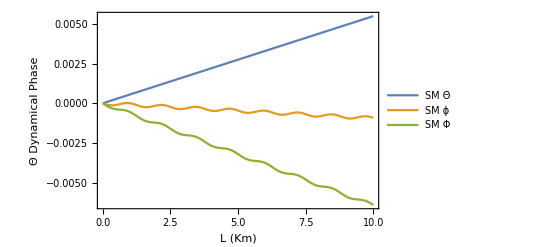

```mathematica
Plot[{ArcTan[Tan[SterileTheta[x,Energy]]],Sterilephi[x,Energy],Sterilephi[x,Energy]-ArcTan[Tan[SterileTheta[x,Energy]]]},{x,0,10},PlotLegends->LineLegend[{"SM Θ","SM ϕ","SM Φ"},LegendFunction->(Framed[#,RoundingRadius->10]&),LabelStyle->{FontSize->7}],PlotRange->All,Frame->True,FrameLabel->{Style["L (Km)",Black,FontSize->10],Style["Θ Dynamical Phase",Black,FontSize->10]},FrameTicksStyle->Black,LabelStyle->{FontSize->12}]
```

```mathematica
SMphi[x,l]
```

tan^-1(0.305044 cos((0.0004805 x)/l)+0.670484 cos((0.00112781 x)/l)+0.0244717 cos((0.00173461 x)/l),-0.305044 sin((0.0004805 x)/l)-0.670484 sin((0.00112781 x)/l)-0.0244717 sin((0.00173461 x)/l))

```mathematica
Sterilephi[x,l]
```

tan^-1(0.305044 cos((0.0004805 x)/l)+0.670484 cos((0.00112781 x)/l)+0.0244717 cos((0.00173461 x)/l)+0.0001 cos((50 x)/l),-0.305044 sin((0.0004805 x)/l)-0.670484 sin((0.00112781 x)/l)-0.0244717 sin((0.00173461 x)/l)-0.0001 sin((50 x)/l))

```mathematica
SMTheta[x,l]
```

(0.000486731 x)/l

```mathematica
SterileTheta[x,l]
```

(0.00548673 x)/l

```mathematica
Em=100000;NMaxValue[{Abs[-SMphi[x,Em]+Sterilephi[x,Em]],0<=x<=100000},x]
```

0.0001

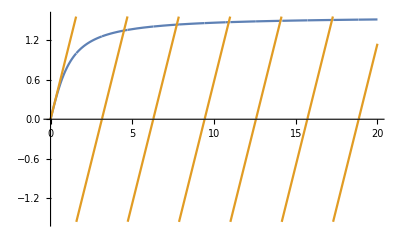

```mathematica
Plot[{ArcTan[x],ArcTan[Tan[x]]},{x,0,20}]
```

### Interval Finding

```mathematica
(*Neutrino oscillation-optimized search*)m1=0.0298;m2=0.031;m3=0.0589;
factor=1.27;

m1sq=m1^2;m2sq=m2^2;m3sq=m3^2;
w1=factor*m1sq;
w2=factor*m2sq;
w3=factor*m3sq;

s1[x_]:=Sin[w1*x];
s2[x_]:=Sin[w2*x];
s3[x_]:=Sin[w3*x];
```

```mathematica
s1[a1]
s2[a1]
s3[a1]
```

sin(0.00112781 a1)

sin(0.00122047 a1)

sin(0.0044059 a1)

```mathematica
a=8.91660312*^6-1.3;s1[a]
s2[a]
s3[a]
```

-0.00174775

-0.0319234

-0.0104006

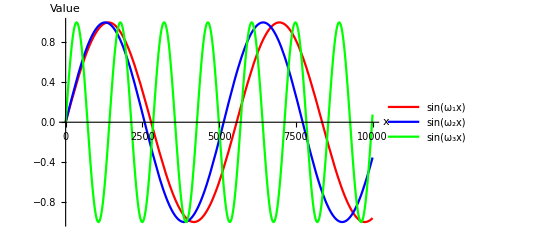

```mathematica
(*Plot around the best zero*)
Plot[{s1[x],s2[x],s3[x]},{x,000,10000},PlotLegends->{"sin(ω₁x)","sin(ω₂x)","sin(ω₃x)"},PlotStyle->{Red,Blue,Green},AxesLabel->{"x","Value"}]
```

```mathematica
c1=π/w1
c2=π/w2
c3=π/w3
```

2785.57

2574.08

713.043

```mathematica
(*Fast linear-time intersection of two sorted interval lists*)FastIntersect[setA_List,setB_List]:=Module[{i=1,j=1,res={},a,b,lo,hi},While[i<=Length[setA]&&j<=Length[setB],a=setA[[i]];b=setB[[j]];
lo=Max[a[[1]],b[[1]]];
hi=Min[a[[2]],b[[2]]];
If[hi>lo,AppendTo[res,{lo,hi}]];
If[a[[2]]<b[[2]],i++,j++];];
res];

(*Example:your parameters*)
nf=100000;
intervals1=Table[{2785.57 n-10,2785.57 n+10},{n,1,nf}];
intervals2=Table[{2574.08 n-10,2574.08 n+10},{n,1,nf}];
intervals3=Table[{713.043 n-1,713.043 n+1},{n,1,nf}];

(*Three-way intersection using fast method*)
intersection3=FastIntersect[FastIntersect[intervals1,intervals2],intervals3];

Length[intersection3]
```

4

```mathematica
intersection3
```

(3.96666×10^6 | 3.96666×10^6
8.9166×10^6 | 8.9166×10^6
1.28833×10^7 | 1.28833×10^7
1.68499×10^7 | 1.68499×10^7)

```mathematica
3.9666592090000003*^6-3.9666572090000003*^6
```

2.

```mathematica
5*3.9666592090000003*^6
```

1.98333×10^7